# SI: numerical checks and theory of inhibition

## Numerical check for SI

```mathematica
Clear["Global`*"];
```

#### Self-consistent solution (more accurate for low secondary nucleation)

```mathematica
solutionselfcons[t_,kappa_,theta_,nc_,lambda_]:=1-(((((kappa*Sqrt[theta+(2/nc)*lambda^2/kappa^2]+Sqrt[kappa^2*(theta+(2/nc)*lambda^2/kappa^2)+lambda^4/kappa^2])/(2kappa))+lambda^2/(2kappa^2))/(((kappa*Sqrt[theta+(2/nc)*lambda^2/kappa^2]+Sqrt[kappa^2*(theta+(2/nc)*lambda^2/kappa^2)+lambda^4/kappa^2])/(2kappa))+lambda^2/(2kappa^2)Exp[kappa*t]))*((((kappa*Sqrt[theta+(2/nc)*lambda^2/kappa^2]-Sqrt[kappa^2*(theta+(2/nc)*lambda^2/kappa^2)+lambda^4/kappa^2])/(2kappa))+lambda^2/(2kappa^2)Exp[kappa*t])/(((kappa*Sqrt[theta+(2/nc)*lambda^2/kappa^2]-Sqrt[kappa^2*(theta+(2/nc)*lambda^2/kappa^2)+lambda^4/kappa^2])/(2kappa))+lambda^2/(2kappa^2))))^(kappa*(theta+(2/nc)*lambda^2/kappa^2)/(Sqrt[kappa^2*(theta+(2/nc)*lambda^2/kappa^2)+lambda^4/kappa^2]))*Exp[-kappa*Sqrt[theta+(2/nc)*lambda^2/kappa^2]*t];

solutionfree[t_,kappa_,theta_,nc_,lambda_,a_,b_]:=1-b/(a+b)*(1-Exp[-(a+b)*t]);
solutionbound[t_,kappa_,theta_,nc_,lambda_,a_,b_]:=b/(a+b)*(1-Exp[-(a+b)*t]);

solutionfreet[t_,kappa_,theta_,nc_,lambda_,a_,b_]:=1-b/(a+b)*(1-Exp[-(a+b)*t])-a/(a+b)+a/(a+b)*(1-solutionselfcons[t,kappa,theta,nc,lambda]);
solutionboundt[t_,kappa_,theta_,nc_,lambda_,a_,b_]:=b/(a+b)*(1-Exp[-(a+b)*t])-b/(a+b)+b/(a+b)*(1-solutionselfcons[t,kappa,theta,nc,lambda]);
```

#### Numerical solution comparison

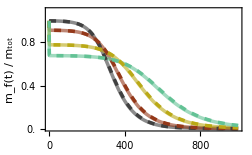

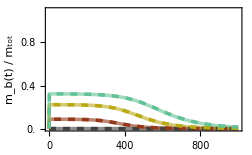

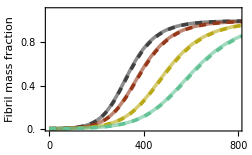

```mathematica
mtot=1.*10^(-6);
kp=3*10^6*60;
kn=1.6*10^(2)*3600/kp;
k2=5.9*10^(10)*3600/kp;
nc=2;
n2=2;
λ=Sqrt[2*kp*kn*mtot^2];
κ=Sqrt[2*kp*k2*mtot^3];
kofffibrils=0;
Keq=1/(21*10^(-6));
kon=1.5*10^(3)*60;
koff=kon/Keq;

i1=2*10^(-6);
i2=6*10^(-6);
i3=10*10^(-6);

equilibriumkappa1=Sqrt[1/(1.+kon*i1/koff)^3]*κ;
equilibriumlambda1=Sqrt[1/(1.+kon*i1/koff)^3]*λ;

equilibriumkappa2=Sqrt[1/(1.+kon*i2/koff)^3]*κ;
equilibriumlambda2=Sqrt[1/(1.+kon*i2/koff)^3]*λ;

equilibriumkappa3=Sqrt[1/(1.+kon*i3/koff)^3]*κ;
equilibriumlambda3=Sqrt[1/(1.+kon*i3/koff)^3]*λ;


(*Numerical solution*)
s=NDSolve[{m'[t]==-(2kp*m[t]-2*kofffibrils)*p[t],p'[t]==kn*m[t]^2+k2*m[t]^2(mtot-m[t]),m[0]==mtot,p[0]==0},{m[t],p[t]},{t,0,1000},MaxStepSize->0.1];

si1=NDSolve[{m'[t]==-(2kp*m[t]-2*kofffibrils)*p[t]-kon*i1*m[t]+koff*mbound[t],p'[t]==kn*m[t]^2+k2*m[t]^2(mtot-m[t]-mbound[t]),mbound'[t]==kon*i1*m[t]-koff*mbound[t],m[0]==mtot,p[0]==0,mbound[0]==0},{m[t],p[t],mbound[t]},{t,0,1000},MaxStepSize->0.1];

si2=NDSolve[{m'[t]==-(2kp*m[t]-2*kofffibrils)*p[t]-kon*i2*m[t]+koff*mbound[t],p'[t]==kn*m[t]^2+k2*m[t]^2(mtot-m[t]-mbound[t]),mbound'[t]==kon*i2*m[t]-koff*mbound[t],m[0]==mtot,p[0]==0,mbound[0]==0},{m[t],p[t],mbound[t]},{t,0,1000},MaxStepSize->0.1];

si3=NDSolve[{m'[t]==-(2kp*m[t]-2*kofffibrils)*p[t]-kon*i3*m[t]+koff*mbound[t],p'[t]==kn*m[t]^2+k2*m[t]^2(mtot-m[t]-mbound[t]),mbound'[t]==kon*i3*m[t]-koff*mbound[t],m[0]==mtot,p[0]==0,mbound[0]==0},{m[t],p[t],mbound[t]},{t,0,1000},MaxStepSize->0.1];


Show[Plot[{Evaluate[((m[t])/mtot)/.s],Evaluate[((m[t])/mtot)/.si1],Evaluate[((m[t])/mtot)/.si2],Evaluate[((m[t])/mtot)/.si3]},{t,0,1000},
BaseStyle->{FontFamily->"Helvetica",FontSize->13},ImageSize->3.5 72,Axes->False,FrameLabel->{"Time (hours)","m_f(t) / m_tot"},Frame->{True,True,False,False},PlotRange->{{0,1000},{-0.0,1.1}},PlotStyle->{{CMYKColor[0,0,0,.75],Opacity[0.6],Thickness[0.01]},{CMYKColor[0,.62,.83,.42],Opacity[0.6],Thickness[0.01]},{CMYKColor[0,.09,.88,.27],Opacity[0.6],Thickness[0.01]},{CMYKColor[0.49,0,.23,.24],Opacity[0.6],Thickness[0.01]}},FrameStyle->Black,
FrameTicks->{{Range[0,1,0.2],None},{Range[0,1000,200],None}}
],Plot[{solutionfreet[t,κ,2/(2*3),2,λ,koff,kon*0],solutionfreet[t,equilibriumkappa1,2/(2*3),2,equilibriumlambda1,koff,kon*i1],solutionfreet[t,equilibriumkappa2,2/(2*3),2,equilibriumlambda2,koff,kon*i2],solutionfreet[t,equilibriumkappa3,2/(2*3),2,equilibriumlambda3,koff,kon*i3]},{t,0,1000},
PlotStyle->{{CMYKColor[0,0,0,.75],Dashed,Thickness[0.01]},{CMYKColor[0,.62,.83,.42],Dashed,Thickness[0.01]},{CMYKColor[0,.09,.88,.27],Dashed,Thickness[0.01]},{CMYKColor[0.49,0,.23,.24],Dashed,Thickness[0.01]}}
]]

Show[Plot[{Evaluate[(0/mtot)/.s],Evaluate[((mbound[t])/mtot)/.si1],Evaluate[((mbound[t])/mtot)/.si2],Evaluate[((mbound[t])/mtot)/.si3]},{t,0,1000},
BaseStyle->{FontFamily->"Helvetica",FontSize->13},ImageSize->3.5 72,Axes->False,FrameLabel->{"Time (hours)","m_b(t) / m_tot"},Frame->{True,True,False,False},PlotRange->{{0,1000},{-0.0,1.1}},PlotStyle->{{CMYKColor[0,0,0,.75],Opacity[0.6],Thickness[0.01]},{CMYKColor[0,.62,.83,.42],Opacity[0.6],Thickness[0.01]},{CMYKColor[0,.09,.88,.27],Opacity[0.6],Thickness[0.01]},{CMYKColor[0.49,0,.23,.24],Opacity[0.6],Thickness[0.01]}},FrameStyle->Black,
FrameTicks->{{Range[0,1,0.2],None},{Range[0,1000,200],None}}
],Plot[{solutionboundt[t,κ,2/(2*3),2,λ,koff,kon*0],solutionboundt[t,equilibriumkappa1,2/(2*3),2,equilibriumlambda1,koff,kon*i1],solutionboundt[t,equilibriumkappa2,2/(2*3),2,equilibriumlambda2,koff,kon*i2],solutionboundt[t,equilibriumkappa3,2/(2*3),2,equilibriumlambda3,koff,kon*i3]},{t,0,1000},PlotStyle->{{CMYKColor[0,0,0,.75],Dashed,Thickness[0.01]},{CMYKColor[0,.62,.83,.42],Dashed,Thickness[0.01]},{CMYKColor[0,.09,.88,.27],Dashed,Thickness[0.01]},{CMYKColor[0.49,0,.23,.24],Dashed,Thickness[0.01]}}
]]

Show[Plot[{Evaluate[((mtot-m[t])/mtot)/.s],Evaluate[((mtot-m[t]-mbound[t])/mtot)/.si1],Evaluate[((mtot-m[t]-mbound[t])/mtot)/.si2],Evaluate[((mtot-m[t]-mbound[t])/mtot)/.si3]},{t,0,1000},
BaseStyle->{FontFamily->"Helvetica",FontSize->13},ImageSize->3.5 72,Axes->False,FrameLabel->{"Time (min)","Fibril mass fraction"},Frame->{True,True,False,False},PlotRange->{{0,800},{-0.0,1.1}},PlotStyle->{{CMYKColor[0,0,0,.75],Opacity[0.6],Thickness[0.01]},{CMYKColor[0,.62,.83,.42],Opacity[0.6],Thickness[0.01]},{CMYKColor[0,.09,.88,.27],Opacity[0.6],Thickness[0.01]},{CMYKColor[0.49,0,.23,.24],Opacity[0.6],Thickness[0.01]}},FrameStyle->Black,
FrameTicks->{{Range[0,1,0.2],None},{Range[0,1000,200],None}}
],Plot[{solutionselfcons[t,κ,2/(2*3),2,λ],solutionselfcons[t,equilibriumkappa1,2/(2*3),2,equilibriumlambda1],solutionselfcons[t,equilibriumkappa2,2/(2*3),2,equilibriumlambda2],solutionselfcons[t,equilibriumkappa3,2/(2*3),2,equilibriumlambda3]},{t,0,1000},PlotStyle->{{CMYKColor[0,0,0,.75],Dashed,Thickness[0.01]},{CMYKColor[0,.62,.83,.42],Dashed,Thickness[0.01]},{CMYKColor[0,.09,.88,.27],Dashed,Thickness[0.01]},{CMYKColor[0.49,0,.23,.24],Dashed,Thickness[0.01]}}]]
```

## Table showing inhibition for different values of kon and koff

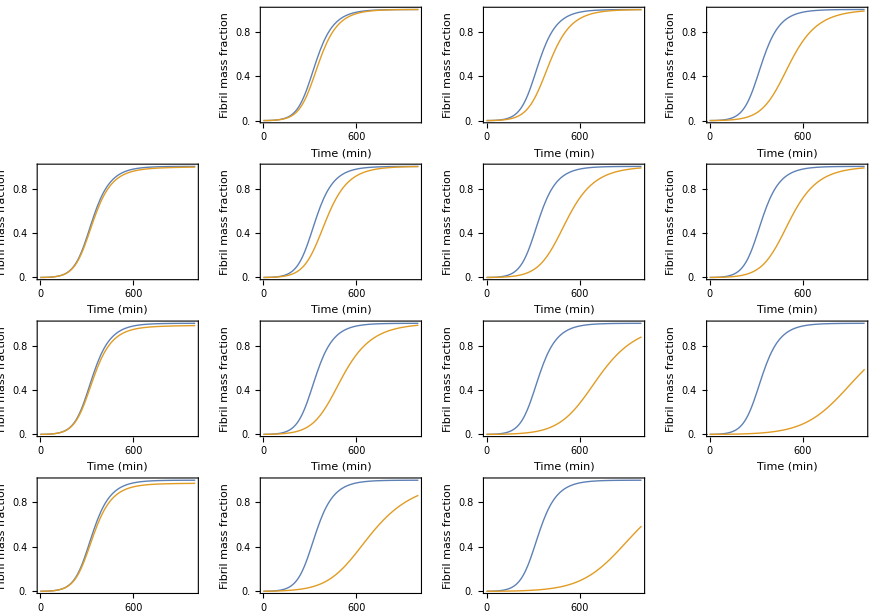

```mathematica
(* Fixed parameters *)
mtot=1.*10^(-6);
kp=3*10^6*60;
kn=1.6*10^(2)*3600/kp;(*5.22*10^5/kp;*)
k2=5.9*10^(10)*3600/kp;(*2.57*10^(14)/kp;*)
nc=2;
n2=2;
λ=Sqrt[2*kp*kn*mtot^2];
κ=Sqrt[2*kp*k2*mtot^3];

(* Relevant parameters to be changed: kon, koff, Keq and Keq with fibrils *)
Keq1=1/(2*10^(-6));
Keq2=1/(3*10^(-6));
Keq3=1/(6*10^(-6));
Keq4=1/(15*10^(-6));
Keq5=1/(50*10^(-6));
i0=2.*10^(-6);
kon1=8.5*10^(-1)*60;
kon2=8.5*10^(1)*60;
kon3=8.5*10^(3)*60;
kon4=8.5*10^(5)*60;
(*koff=kon/Keq;*)

s=NDSolve[{m'[t]==-2(kp*m[t])*p[t],p'[t]==kn*m[t]^2+k2*m[t]^2(mtot-m[t]),m[0]==mtot,p[0]==0},{m[t],p[t]},{t,0,1000},MaxStepSize->0.1];

si13=NDSolve[{m'[t]==-2(kp*m[t])*p[t]-kon1*i0*m[t]+kon1/Keq3*mbound[t],p'[t]==kn*m[t]^2+k2*m[t]^2(mtot-m[t]-mbound[t]),mbound'[t]==kon1*i0*m[t]-kon1/Keq3*mbound[t],m[0]==mtot,p[0]==0,mbound[0]==0},{m[t],p[t],mbound[t]},{t,0,1000},MaxStepSize->0.1];
si14=NDSolve[{m'[t]==-2(kp*m[t])*p[t]-kon1*i0*m[t]+kon1/Keq4*mbound[t],p'[t]==kn*m[t]^2+k2*m[t]^2(mtot-m[t]-mbound[t]),mbound'[t]==kon1*i0*m[t]-kon1/Keq4*mbound[t],m[0]==mtot,p[0]==0,mbound[0]==0},{m[t],p[t],mbound[t]},{t,0,1000},MaxStepSize->0.1];
si15=NDSolve[{m'[t]==-2(kp*m[t])*p[t]-kon1*i0*m[t]+kon1/Keq5*mbound[t],p'[t]==kn*m[t]^2+k2*m[t]^2(mtot-m[t]-mbound[t]),mbound'[t]==kon1*i0*m[t]-kon1/Keq5*mbound[t],m[0]==mtot,p[0]==0,mbound[0]==0},{m[t],p[t],mbound[t]},{t,0,1000},MaxStepSize->0.1];

si22=NDSolve[{m'[t]==-2(kp*m[t])*p[t]-kon2*i0*m[t]+kon2/Keq2*mbound[t],p'[t]==kn*m[t]^2+k2*m[t]^2(mtot-m[t]-mbound[t]),mbound'[t]==kon2*i0*m[t]-kon2/Keq2*mbound[t],m[0]==mtot,p[0]==0,mbound[0]==0},{m[t],p[t],mbound[t]},{t,0,1000},MaxStepSize->0.1];
si23=NDSolve[{m'[t]==-2(kp*m[t])*p[t]-kon2*i0*m[t]+kon2/Keq3*mbound[t],p'[t]==kn*m[t]^2+k2*m[t]^2(mtot-m[t]-mbound[t]),mbound'[t]==kon2*i0*m[t]-kon2/Keq3*mbound[t],m[0]==mtot,p[0]==0,mbound[0]==0},{m[t],p[t],mbound[t]},{t,0,1000},MaxStepSize->0.1];
si24=NDSolve[{m'[t]==-2(kp*m[t])*p[t]-kon2*i0*m[t]+kon2/Keq4*mbound[t],p'[t]==kn*m[t]^2+k2*m[t]^2(mtot-m[t]-mbound[t]),mbound'[t]==kon2*i0*m[t]-kon2/Keq4*mbound[t],m[0]==mtot,p[0]==0,mbound[0]==0},{m[t],p[t],mbound[t]},{t,0,1000},MaxStepSize->0.1];
si25=NDSolve[{m'[t]==-2(kp*m[t])*p[t]-kon2*i0*m[t]+kon2/Keq5*mbound[t],p'[t]==kn*m[t]^2+k2*m[t]^2(mtot-m[t]-mbound[t]),mbound'[t]==kon2*i0*m[t]-kon2/Keq5*mbound[t],m[0]==mtot,p[0]==0,mbound[0]==0},{m[t],p[t],mbound[t]},{t,0,1000},MaxStepSize->0.1];

si31=NDSolve[{m'[t]==-2(kp*m[t])*p[t]-kon3*i0*m[t]+kon3/Keq1*mbound[t],p'[t]==kn*m[t]^2+k2*m[t]^2(mtot-m[t]-mbound[t]),mbound'[t]==kon3*i0*m[t]-kon3/Keq1*mbound[t],m[0]==mtot,p[0]==0,mbound[0]==0},{m[t],p[t],mbound[t]},{t,0,1000},MaxStepSize->0.1];
si32=NDSolve[{m'[t]==-2(kp*m[t])*p[t]-kon3*i0*m[t]+kon3/Keq2*mbound[t],p'[t]==kn*m[t]^2+k2*m[t]^2(mtot-m[t]-mbound[t]),mbound'[t]==kon3*i0*m[t]-kon3/Keq2*mbound[t],m[0]==mtot,p[0]==0,mbound[0]==0},{m[t],p[t],mbound[t]},{t,0,1000},MaxStepSize->0.1];
si33=NDSolve[{m'[t]==-2(kp*m[t])*p[t]-kon3*i0*m[t]+kon3/Keq3*mbound[t],p'[t]==kn*m[t]^2+k2*m[t]^2(mtot-m[t]-mbound[t]),mbound'[t]==kon3*i0*m[t]-kon3/Keq3*mbound[t],m[0]==mtot,p[0]==0,mbound[0]==0},{m[t],p[t],mbound[t]},{t,0,1000},MaxStepSize->0.1];
si34=NDSolve[{m'[t]==-2(kp*m[t])*p[t]-kon3*i0*m[t]+kon3/Keq4*mbound[t],p'[t]==kn*m[t]^2+k2*m[t]^2(mtot-m[t]-mbound[t]),mbound'[t]==kon3*i0*m[t]-kon3/Keq4*mbound[t],m[0]==mtot,p[0]==0,mbound[0]==0},{m[t],p[t],mbound[t]},{t,0,1000},MaxStepSize->0.1];

si41=NDSolve[{m'[t]==-2(kp*m[t])*p[t]-kon4*i0*m[t]+kon4/Keq1*mbound[t],p'[t]==kn*m[t]^2+k2*m[t]^2(mtot-m[t]-mbound[t]),mbound'[t]==kon4*i0*m[t]-kon4/Keq1*mbound[t],m[0]==mtot,p[0]==0,mbound[0]==0},{m[t],p[t],mbound[t]},{t,0,1000},MaxStepSize->0.1];
si42=NDSolve[{m'[t]==-2(kp*m[t])*p[t]-kon4*i0*m[t]+kon4/Keq2*mbound[t],p'[t]==kn*m[t]^2+k2*m[t]^2(mtot-m[t]-mbound[t]),mbound'[t]==kon4*i0*m[t]-kon4/Keq2*mbound[t],m[0]==mtot,p[0]==0,mbound[0]==0},{m[t],p[t],mbound[t]},{t,0,1000},MaxStepSize->0.1];
si43=NDSolve[{m'[t]==-2(kp*m[t])*p[t]-kon4*i0*m[t]+kon4/Keq3*mbound[t],p'[t]==kn*m[t]^2+k2*m[t]^2(mtot-m[t]-mbound[t]),mbound'[t]==kon4*i0*m[t]-kon4/Keq3*mbound[t],m[0]==mtot,p[0]==0,mbound[0]==0},{m[t],p[t],mbound[t]},{t,0,1000},MaxStepSize->0.1];

plot13=Plot[{Evaluate[((mtot-m[t])/mtot)/.s],Evaluate[((mtot-m[t]-mbound[t])/mtot)/.si13]},{t,0,1000},PlotRange->{All,{0,1}},PlotStyle->{Thick,Thick,Dashed,Dashed,Dashed,Dashed},AspectRatio->0.7,ImageSize->200,PlotStyle->{Thick,Dashed,Dashed},Axes->False,FrameLabel->{"Time (min)","Fibril mass fraction"},Frame->True,BaseStyle->{FontFamily->"PT Sans",FontSize->12},PlotRange->{{0,10},{-0.0,1.05}},FrameStyle->Black,FrameTicks->{{Range[0,1,0.2],None},{Range[0,1000,200],None}}];
plot14=Plot[{Evaluate[((mtot-m[t])/mtot)/.s],Evaluate[((mtot-m[t]-mbound[t])/mtot)/.si14]},{t,0,1000},PlotRange->{All,{0,1}},PlotStyle->{Thick,Thick,Dashed,Dashed,Dashed,Dashed},AspectRatio->0.7,ImageSize->200,PlotStyle->{Thick,Dashed,Dashed},BaseStyle->{FontFamily->"PT Sans",FontSize->10},Axes->False,FrameLabel->{"Time (min)","Fibril mass fraction"},Frame->True,BaseStyle->{FontFamily->"PT Sans",FontSize->12},PlotRange->{{0,10},{-0.0,1.05}},FrameStyle->Black,FrameTicks->{{Range[0,1,0.2],None},{Range[0,1000,200],None}}];
plot15=Plot[{Evaluate[((mtot-m[t])/mtot)/.s],Evaluate[((mtot-m[t]-mbound[t])/mtot)/.si15]},{t,0,1000},PlotRange->{All,{0,1}},PlotStyle->{Thick,Thick,Dashed,Dashed,Dashed,Dashed},AspectRatio->0.7,ImageSize->200,PlotStyle->{Thick,Dashed,Dashed},BaseStyle->{FontFamily->"PT Sans",FontSize->10},Axes->False,FrameLabel->{"Time (min)","Fibril mass fraction"},Frame->True,BaseStyle->{FontFamily->"PT Sans",FontSize->12},PlotRange->{{0,10},{-0.0,1.05}},FrameStyle->Black,FrameTicks->{{Range[0,1,0.2],None},{Range[0,1000,200],None}}];

plot22=Plot[{Evaluate[((mtot-m[t])/mtot)/.s],Evaluate[((mtot-m[t]-mbound[t])/mtot)/.si22]},{t,0,1000},PlotRange->{All,{0,1}},PlotStyle->{Thick,Thick,Dashed,Dashed,Dashed,Dashed},AspectRatio->0.7,ImageSize->200,PlotStyle->{Thick,Dashed,Dashed},BaseStyle->{FontFamily->"PT Sans",FontSize->10},Axes->False,FrameLabel->{"Time (min)","Fibril mass fraction"},Frame->True,BaseStyle->{FontFamily->"PT Sans",FontSize->12},PlotRange->{{0,10},{-0.0,1.05}},FrameStyle->Black,FrameTicks->{{Range[0,1,0.2],None},{Range[0,1000,200],None}}];
plot23=Plot[{Evaluate[((mtot-m[t])/mtot)/.s],Evaluate[((mtot-m[t]-mbound[t])/mtot)/.si23]},{t,0,1000},PlotRange->{All,{0,1}},PlotStyle->{Thick,Thick,Dashed,Dashed,Dashed,Dashed},AspectRatio->0.7,ImageSize->200,PlotStyle->{Thick,Dashed,Dashed},BaseStyle->{FontFamily->"PT Sans",FontSize->10},Axes->False,FrameLabel->{"Time (min)","Fibril mass fraction"},Frame->True,BaseStyle->{FontFamily->"PT Sans",FontSize->12},PlotRange->{{0,10},{-0.0,1.05}},FrameStyle->Black,FrameTicks->{{Range[0,1,0.2],None},{Range[0,1000,200],None}}];
plot24=Plot[{Evaluate[((mtot-m[t])/mtot)/.s],Evaluate[((mtot-m[t]-mbound[t])/mtot)/.si24]},{t,0,1000},PlotRange->{All,{0,1}},PlotStyle->{Thick,Thick,Dashed,Dashed,Dashed,Dashed},AspectRatio->0.7,ImageSize->200,PlotStyle->{Thick,Dashed,Dashed},BaseStyle->{FontFamily->"PT Sans",FontSize->10},Axes->False,FrameLabel->{"Time (min)","Fibril mass fraction"},Frame->True,BaseStyle->{FontFamily->"PT Sans",FontSize->12},PlotRange->{{0,10},{-0.0,1.05}},FrameStyle->Black,FrameTicks->{{Range[0,1,0.2],None},{Range[0,1000,200],None}}];
plot25=Plot[{Evaluate[((mtot-m[t])/mtot)/.s],Evaluate[((mtot-m[t]-mbound[t])/mtot)/.si25]},{t,0,1000},PlotRange->{All,{0,1}},PlotStyle->{Thick,Thick,Dashed,Dashed,Dashed,Dashed},AspectRatio->0.7,ImageSize->200,PlotStyle->{Thick,Dashed,Dashed},BaseStyle->{FontFamily->"PT Sans",FontSize->10},Axes->False,FrameLabel->{"Time (min)","Fibril mass fraction"},Frame->True,BaseStyle->{FontFamily->"PT Sans",FontSize->12},PlotRange->{{0,10},{-0.0,1.05}},FrameStyle->Black,FrameTicks->{{Range[0,1,0.2],None},{Range[0,1000,200],None}}];

plot31=Plot[{Evaluate[((mtot-m[t])/mtot)/.s],Evaluate[((mtot-m[t]-mbound[t])/mtot)/.si31]},{t,0,1000},PlotRange->{All,{0,1}},PlotStyle->{Thick,Thick,Dashed,Dashed,Dashed,Dashed},AspectRatio->0.7,ImageSize->200,PlotStyle->{Thick,Dashed,Dashed},BaseStyle->{FontFamily->"PT Sans",FontSize->10},Axes->False,FrameLabel->{"Time (min)","Fibril mass fraction"},Frame->True,BaseStyle->{FontFamily->"PT Sans",FontSize->12},PlotRange->{{0,10},{-0.0,1.05}},FrameStyle->Black,FrameTicks->{{Range[0,1,0.2],None},{Range[0,1000,200],None}}];
plot32=Plot[{Evaluate[((mtot-m[t])/mtot)/.s],Evaluate[((mtot-m[t]-mbound[t])/mtot)/.si32]},{t,0,1000},PlotRange->{All,{0,1}},PlotStyle->{Thick,Thick,Dashed,Dashed,Dashed,Dashed},AspectRatio->0.7,ImageSize->200,PlotStyle->{Thick,Dashed,Dashed},BaseStyle->{FontFamily->"PT Sans",FontSize->10},Axes->False,FrameLabel->{"Time (min)","Fibril mass fraction"},Frame->True,BaseStyle->{FontFamily->"PT Sans",FontSize->12},PlotRange->{{0,10},{-0.0,1.05}},FrameStyle->Black,FrameTicks->{{Range[0,1,0.2],None},{Range[0,1000,200],None}}];
plot33=Plot[{Evaluate[((mtot-m[t])/mtot)/.s],Evaluate[((mtot-m[t]-mbound[t])/mtot)/.si33]},{t,0,1000},PlotRange->{All,{0,1}},PlotStyle->{Thick,Thick,Dashed,Dashed,Dashed,Dashed},AspectRatio->0.7,ImageSize->200,PlotStyle->{Thick,Dashed,Dashed},BaseStyle->{FontFamily->"PT Sans",FontSize->10},Axes->False,FrameLabel->{"Time (min)","Fibril mass fraction"},Frame->True,BaseStyle->{FontFamily->"PT Sans",FontSize->12},PlotRange->{{0,10},{-0.0,1.05}},FrameStyle->Black,FrameTicks->{{Range[0,1,0.2],None},{Range[0,1000,200],None}}];
plot34=Plot[{Evaluate[((mtot-m[t])/mtot)/.s],Evaluate[((mtot-m[t]-mbound[t])/mtot)/.si34]},{t,0,1000},PlotRange->{All,{0,1}},PlotStyle->{Thick,Thick,Dashed,Dashed,Dashed,Dashed},AspectRatio->0.7,ImageSize->200,PlotStyle->{Thick,Dashed,Dashed},BaseStyle->{FontFamily->"PT Sans",FontSize->10},Axes->False,FrameLabel->{"Time (min)","Fibril mass fraction"},Frame->True,BaseStyle->{FontFamily->"PT Sans",FontSize->12},PlotRange->{{0,10},{-0.0,1.05}},FrameStyle->Black,FrameTicks->{{Range[0,1,0.2],None},{Range[0,1000,200],None}}];

plot41=Plot[{Evaluate[((mtot-m[t])/mtot)/.s],Evaluate[((mtot-m[t]-mbound[t])/mtot)/.si41]},{t,0,1000},PlotRange->{All,{0,1}},PlotStyle->{Thick,Thick,Dashed,Dashed,Dashed,Dashed},AspectRatio->0.7,ImageSize->200,PlotStyle->{Thick,Dashed,Dashed},BaseStyle->{FontFamily->"PT Sans",FontSize->10},Axes->False,FrameLabel->{"Time (min)","Fibril mass fraction"},Frame->True,BaseStyle->{FontFamily->"PT Sans",FontSize->12},PlotRange->{{0,10},{-0.0,1.05}},FrameStyle->Black,FrameTicks->{{Range[0,1,0.2],None},{Range[0,1000,200],None}}];
plot42=Plot[{Evaluate[((mtot-m[t])/mtot)/.s],Evaluate[((mtot-m[t]-mbound[t])/mtot)/.si42]},{t,0,1000},PlotRange->{All,{0,1}},PlotStyle->{Thick,Thick,Dashed,Dashed,Dashed,Dashed},AspectRatio->0.7,ImageSize->200,PlotStyle->{Thick,Dashed,Dashed},BaseStyle->{FontFamily->"PT Sans",FontSize->10},Axes->False,FrameLabel->{"Time (min)","Fibril mass fraction"},Frame->True,BaseStyle->{FontFamily->"PT Sans",FontSize->12},PlotRange->{{0,10},{-0.0,1.05}},FrameStyle->Black,FrameTicks->{{Range[0,1,0.2],None},{Range[0,1000,200],None}}];
plot43=Plot[{Evaluate[((mtot-m[t])/mtot)/.s],Evaluate[((mtot-m[t]-mbound[t])/mtot)/.si43]},{t,0,1000},PlotRange->{All,{0,1}},PlotStyle->{Thick,Thick,Dashed,Dashed,Dashed,Dashed},AspectRatio->0.7,ImageSize->200,PlotStyle->{Thick,Dashed,Dashed},BaseStyle->{FontFamily->"PT Sans",FontSize->10},Axes->False,FrameLabel->{"Time (min)","Fibril mass fraction"},Frame->True,BaseStyle->{FontFamily->"PT Sans",FontSize->12},PlotRange->{{0,10},{-0.0,1.05}},FrameStyle->Black,FrameTicks->{{Range[0,1,0.2],None},{Range[0,1000,200],None}}];


GraphicsGrid[{{x,plot25,plot34,plot43},{plot15,plot24,plot33,plot43},{plot14,plot23,plot32,plot41},{plot13,plot22,plot31,x}}]
```

#### Export data as xls

```mathematica
m0=Table[{t,Evaluate[((mtot-m[t])/mtot)/.s],Evaluate[((mtot-m[t]-mbound[t])/mtot)/.si13],Evaluate[((mtot-m[t]-mbound[t])/mtot)/.si22],Evaluate[((mtot-m[t]-mbound[t])/mtot)/.si31],Evaluate[((mtot-m[t]-mbound[t])/mtot)/.si14],Evaluate[((mtot-m[t]-mbound[t])/mtot)/.si23],Evaluate[((mtot-m[t]-mbound[t])/mtot)/.si32],Evaluate[((mtot-m[t]-mbound[t])/mtot)/.si41],Evaluate[((mtot-m[t]-mbound[t])/mtot)/.si15],Evaluate[((mtot-m[t]-mbound[t])/mtot)/.si24],Evaluate[((mtot-m[t]-mbound[t])/mtot)/.si33],Evaluate[((mtot-m[t]-mbound[t])/mtot)/.si42],Evaluate[((mtot-m[t]-mbound[t])/mtot)/.si25],Evaluate[((mtot-m[t]-mbound[t])/mtot)/.si34],Evaluate[((mtot-m[t]-mbound[t])/mtot)/.si43]},{t,0,1000,1}];
m0//TableForm;

Export["Datatable.xls",m0,"XLS"]
```

Datatable.xls